## 什么是 Mathematica 核心语言

我们已经看到，虽然 Mathematica 提供了一些函数可以让我们像编写 C 程序一样编写 Mathematica 程序，但是这样编出来的程序的效率很成问题，而且程序本身也不易懂。另一方面，我们还展示了如何用所谓 Mathematica 核心语言编制出更高效、更简明的程序。例如上次课最后的例子：

```mathematica
myPrimeSum2=Plus@@Prime/@Range[PrimePi[#]]&;
```

这里有很多像乱码一样的东西（@@、/@、#、&），它们其实只是一些 Mathematica 内建函数的简写形式，其完整形式还是很好看的：

```mathematica
myPrimeSum2=Function[n,Apply[Plus,Map[Prime,Range[PrimePi[n]]]]];
```

Mathematica 的核心语言与 C 语言的本质区别在于它们的范式：C 语言是命令式的，或者说面向过程的；而 Mathematica 是函数式的。它们之间的区别比 C 和 C++、Java 等面向对象语言之间的区别还要大。按照范式分类的话， Mathematica 更像 Lisp、Haskell 和 OCaml 等语言。

为了解释清楚 Mathematica 核心语言的基本原理，我们有必要研究一下 Stephen Wolfram 到底是如何写出 Mathematica 的。关于这个问题，我推荐一份有趣的文档：

The Mathematica Story: A Scrapbook
		https://www.wolfram.com/mathematica/scrapbook/

在这里你可以看到很多 Mathematica 发展史上的珍贵手稿和照片，其中就包含有 Wolfram 当年如何发明 Mathematica 的线索。

Wolfram 原本是学理论物理的，在他的研究中需要做很多复杂的计算。最初是手算，后来开始用计算机。在当时，只有一款计算机代数系统可用，这就是由 MIT 计算机科学与人工智能实验室开发的 Macsyma（Project MAC's SYmbolic MAnipulator，简称 Macsyma）。Wolfram 对 Macsyma 并不满意 ，所以用了几年之后，他开始开发自己的计算机代数系统，这就是后来的 Mathematica。

Mathematica 是用 C 语言编写的，所以运算符的使用习惯、以及条件、循环等控制结构的名字都与 C 语言很像。

Macsyma 是用 MAC Lisp 实现的，要用它实现一些复杂的计算必须深入到它的源程序中，所以不懂 Lisp 语言是不行的。 Wolfram 因此受到 Lisp 的很多影响，Mathematica 的核心语言中与 Lisp 相似的部分就由此而来。

Lisp（LISt Processing，简称 Lisp）是第二古老的高级程序语言（最老的是 Fortran，仅比 Lisp 大一岁），它由 John McCarthy 于 1958 年发明。

（Steve Jobs，2011年10月5日逝世；Dennis Ritchie，2011年10月12日逝世；John McCarthy，2011年10月24日逝世。）

Lisp 的含义是"表处理"，所谓"表"，就是形如

(item1 item2 item3)

的一个对象，它也叫做 S-表达式（S-expression，Symbolic expression 的简称）。

Lisp 源程序由一系列这样的表嵌套而成：

(item1 (item2 ((item3 item4 item5) item6) (item7 item8)))

一个 Lisp 解释器的目标就是求出传递给它的 S-表达式的值。求值的规则是，每个表的第一个条目被认为是函数名，其它条目则被认为是这个函数的自变量。例如，表 (+ 2 2) 的值是 2+2=4，而表

(+ (+ 2 2) (* 3 5))

的值是 (2+2)+(3×5)=19。

Lisp 的这种运算表示法叫做波兰前缀记法，是波兰数学家 Jan Łukasiewicz 发明的。这种记法多多少少有些反人类，但是却非常便于计算机处理。

事实上，这样的表达式很容易通过图论中“树”的概念来表达：函数即节点，自变量即分支。

在编译原理中，编译的第一步是将源程序转化为抽象语法树（Abstract Syntax Tree，简称 AST）。Lisp 的这种语法可以认为是在直接书写语法树。

在 Mathematica 中，我们可以用 TreeForm 来获得一个表达式的语法树。

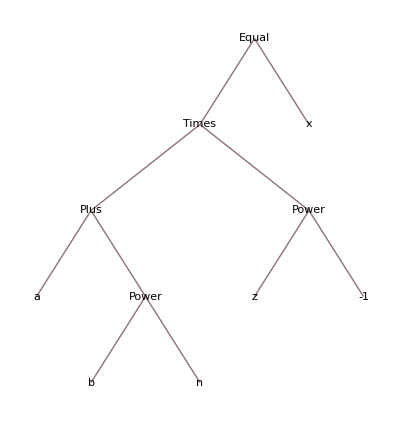

```mathematica
TreeForm[(a+b^n)/z==x]
```

这样的一棵树按照 Lisp 的写法则是：

(= (* (+ a (expt b n)) (expt z -1)) x)

事实上，Mathematica 的内核程序也是这样理解所有表达式的，我们可以用 FullForm 来获得一个表达式在 Mathematica 内部的完整形式:

```mathematica
FullForm[(a+b^n)/z==x]
```

Equal[Times[Plus[a,Power[b,n]],Power[z,-1]],x]

我们可以看到，Mathematica 和 Lisp 的区别仅在于，Lisp 中的函数表示为

(函数名　参数1　参数2)

而 Mathematica 中的函数表示为

函数名[参数1, 参数2]

在 Mathematica 中，满足如下条件的对象就叫做表达式（expression）：

原子对象是表达式；

若 F、X1、X2、…、Xn 是表达式，则 F[X1, X2, …, Xn] 也是表达式。

Mathematica 中的一切对象都是表达式，一个 Mathematica 程序就是一个表达式。

```mathematica
FullForm/@{a+b,a-b,a*b,a/b,a^b,a==b,a!=b,a<b,a<=b,a>b,a>=b,a&&b,a||b} (* 常见运算符的完整形式 *)
```

```mathematica
ForAll[ϵ,ϵ>0,Exists[δ,δ>0,ForAll[x,Abs[x-Subscript[x, 0]]<δ,Abs[f[x]-f[Subscript[x, 0]]]<ϵ]]]//TraditionalForm
```

∀_(ϵ,ϵ>0)∃_(δ,δ>0)∀_(x,Abs[x-x_0]<δ)Abs[f(x)-f(x_0)]<ϵ

这一事实如此地重要，以至于有人将它称为 Mathematica 的第一原理。

Mathematica 第一原理：万物皆表（达式）。

第一原理关注的仅仅是被计算对象的表示法，它尚未涉及计算本身。Lisp 并不擅长计算，我想这也是 Wolfram 对 Macsyma 和 Lisp 不满意的原因。Mathematica 的计算思想来自于其它函数式语言，如 Haskell、OCaml 等等。要理解这种思想，我们先回忆一下人类是如何计算的。

```mathematica
Trace[(#2-#1)&@@(Integrate[Sin[x]^2,x]/.{x->#}&/@{0,2Pi})]
```

{{(∫Sin[x]^2 ⅆx/.{x→#1}&)/@{0,2 π},{(∫Sin[x]^2 ⅆx/.{x→#1}&)[0],(∫Sin[x]^2 ⅆx/.{x→#1}&)[2 π]},{(∫Sin[x]^2 ⅆx/.{x→#1}&)[0],∫Sin[x]^2 ⅆx/.{x→0},{∫Sin[x]^2 ⅆx,x/2-1/4 Sin[2 x]},{{x→0,x→0},{x→0}},x/2-1/4 Sin[2 x]/.{x→0},0/2-1/4 Sin[2 0],{0/2,0},{{{2 0,0},Sin[0],0},-0/4,0},0+0,0},{(∫Sin[x]^2 ⅆx/.{x→#1}&)[2 π],∫Sin[x]^2 ⅆx/.{x→2 π},{∫Sin[x]^2 ⅆx,x/2-1/4 Sin[2 x]},{{x→2 π,x→2 π},{x→2 π}},x/2-1/4 Sin[2 x]/.{x→2 π},(2 π)/2-1/4 Sin[2 (2 π)],{(2 π)/2,(2 π)/2,π},{{{2 (2 π),2 2 π,4 π},Sin[4 π],0},-0/4,0},π+0,π},{0,π}},(#2-#1&)@@{0,π},(#2-#1&)[0,π],π-0,{-0,0},π+0,π}

仔细分析这个过程可以发现，在每一步里我们做的其实都是下面这两件事：

从待计算对象中识别一些可化简的模式

将识别出的模式用已知的规则进行化简

Mathematica 也是这样进行计算的，其中第一步叫做模式匹配，第二步叫做规则代入。基于模式和规则的计算模型在数理逻辑或者计算机科学中叫重写系统（rewriting system）。

Mathematica 第二原理：计算即重写。

Lisp 没有重写系统、Haskell、OCaml 不符合万物皆表，但是人们还是将它们归为一类，称为函数式语言。这是因为这些语言拥有一个共同的原理，那就是把函数视为最基本的、可操作的对象。

在 Lisp 中，我们可以通过在一个表前加“'”标记的办法来制止 Lisp 解释器对它求值，这样被制止了的表被认为是某种可操作的数据。当我们将一些数据组合成一个表 L 之后，可以通过 (eval L) 强制性地求 L 的值，此时数据 L 被转化成了可执行的代码。“代码即数据（Code-as-Data）”被称为 Lisp 的哲学。

在 Haskell 中，每种类型可以视为一个集合，类型之间的函数则成为集合间的映射。映射 f: X→Y 和 g: Y→Z 的复合 g.f: X→Z 可以很容易地通过 Haskell 的“.”运算符得到。注意从集合 Y 到集合 Z 的映射全体 Z^Y 也是一个集合，这个集合在 Haskell 语言中自动定义了一个新的类型。于是任何二元函数 f: X×Y→Z 都可视为一个从 X 到 Z^Y 的一元函数，记为f: X→(Y→Z)，这种对应被称为函数的 currying。（Haskell和Curry分别是数理逻辑学家Haskell Brooks Curry的名和姓，事实上还有两个编程语言分别叫Brook和Curry。）

在 Mathematica 中既可以实现“代码即数据”这种 Lisp 哲学，也可以实现复合和 currying 等函数上的运算，所以人们才将它与 Lisp、Haskell 等语言归在一类。Mathematica 的这一特征是如此重要，以至于我们要将它总结为第零原理。

Mathematica 第零原理：重要的是函数，而非变量。

Mathematica 核心语言中还有关于模块化编程的一些内容。这些内容并非某种原理，而是为了构建大型程序而不得不从其它语言中引入的特性：模块与作用域的概念广泛存在于各种程序语言中；而Mathematica 的“语境（context）”概念非常像 C++ 中的“命名空间（namespace）”。

以上就是 Mathematica 核心语言的主要内容：表达式、重写系统、泛函编程和模块化。这也将是我们在本课程中学到的东西。

## 表达式与表

根据定义，一个表达式或者是原子，或者是形如 F[X1, X2, …, Xn] 的函数。事实上，原子也可以看成后者的特殊情况，只要我们把函数的自变量个数取成零就行了。所以，以后我们讨论表达式的时候，总把它写成 F[X1, X2, …, Xn] 的样子。

给定一个表达式 F[X1, X2, …, Xn]，我们称 F 是它的“头”。

```mathematica
Head/@{1,1/2,True,"number",a+b,a-b,a*b,a/b,(f+g)[x1,x2,x3]}
```

（运算符 /@ 的全名叫 Map，是最常用的泛函运算之一。用它可以方便地测试一个函数在一组变量上的作用效果，而不必把这个函数名写很多次。）

```mathematica
h/@k[x1,x2,x3]
```

我们发现对于原子表达式：符号的头总是 Symbol；数字的头则依赖于它的类型，结果可以是 Integer、Rational、Real 和 Complex；字符串的头总是 String；图片的头是 Image 等等。

利用这个性质，我们可以判断一个表达式是否是原子。

```mathematica
myAtomQ=Function[ex,MemberQ[{Symbol,Integer,Rational,Reals,Complex,String,Image},Head[ex]]];
```

我们的函数 myAtomQ 与系统内建函数 AtomQ 有差不多的功能。

除了头以外，我们也常常需要将表达式的参数部分取出来。取出来的东西是一些表达式构成的序列，是没有头的。但是在 Mathematica 里所有的表达式都必须有头，所以，为了处理这种无头表达式，Mathematica 引入表（List）这个概念，然后规定所有的无头表达式的头都是 List。

```mathematica
ex=f[x1,x2,x3];
List@@ex
```

表达式 X1, X2,…, Xn 构成的表记为 {X1, X2,…, Xn}。

List 本身也是 Mathematica 的一个内部函数，它的作用是将输入的表达式序列做成一个表。

```mathematica
List[1,2,3]
```

熟悉面向对象编程的同学可以发现，如果把 List 视为类（class），那么 List 函数就是这个类的构造函数（constructor）。

让我们再回到表达式 F[X1, X2, …, Xn] 。现在我们知道，它的头以外的部分可以用 List[X1, X2,…, Xn] 来表示。所以这样一个操作可以简单地认为是将原表达式的头 F 换成了系统内建符号 List。

换头术也是 Mathematica 中最常用的泛函运算之一，它的全名叫 Apply，简写形式为 @@。

```mathematica
Apply[g,h[x1,x2,x3]]
g@@h[x1,x2,x3]
```

表这种表达式还有一种变体，叫做序列（Sequence）。序列可以认为是没有两边花括号（“{”和“}”）的表，或者说，表是用序列的元素做成了一个新的对象，而序列是某种更原始的东西。

```mathematica
ex=h[1,2,3]
seq=Sequence@@ex
lst=List@@ex
```

```mathematica
f[seq]
f[lst]
f@@lst
f[seq,lst,4,5,6]
```

上面的例子表明，当我们想把一个表达式的参数传递给另一个函数时，用 List 换头的结果可能不是我们想要的，因为多了一层花括号。如果不想要这层花括号，就要用 Sequence 换头。

除了用 Head 和 Apply 以外，Mathematica 还提供了另一种访问复合表达式内部表达式的方法，即系统内建函数 Part，简写形式为 [[…]]。

```mathematica
ex=f[x1,x2,x3];
{ex[[0]],ex[[1]],ex[[2]],ex[[3]],ex[[4]]}
```

对于嵌套的表达式，我们可以多次地取 Part：

```mathematica
ex=f[a,g[b,c],h[d,k[e,i],j]];
ex[[3]][[2]][[2]]
```

这个操作可以直接通过一个 Part 来完成：

```mathematica
ex[[3,2,2]]
```

Part 还有很多其它的变体，详见帮助系统。

```mathematica
ex[[-1,-2,-1]]
ex[[{2,3}]]
ex[[1;;2]]
ex[[1;;3;;2]]
```

最常用的一些 Part 有属于它们自己的内建函数：

```mathematica
Function[op,op[f[x1,x2,x3,x4]]]/@{First,Last,Rest,Most}
Take[f[x1,x2,x3,x4],{2,3}]
Drop[f[x1,x2,x3,x4],{2,3}]
```

对于给定的表达式，有两个值很重要，即它的长度和深度：

```mathematica
Length[f[g[x1,h[x2,x3]],x4]]
Depth[f[g[x1,h[x2,x3]],x4]]
```

表的构造：

```mathematica
Range[10]
Range[2,10]
Range[2,10,3]
```

```mathematica
Table[i^2+i+1,{i,10}]
Table[KroneckerDelta[i,j-1]+t KroneckerDelta[i,j+4],{i,5},{j,5}]//MatrixForm
```

```mathematica
Array[#^2+#+1&,10]
#^2+#+1&/@Range[10]
```

```mathematica
Array[f,5,2,h]
```

```mathematica
Tuples[Range[3],3]
Outer[f,Range[3],Range[2]]//MatrixForm
```

查询和搜索：

```mathematica
ex=f[x1,x2,x3,x4];
Function[i,MemberQ[ex,i]]/@{f,x1,x2,x3,x4,x5,x6}
Function[i,FreeQ[ex,i]]/@{f,x1,x2,x3,x4,x5,x6}
```

```mathematica
MemberQ[ex,f,Heads->True]
```

```mathematica
FreeQ[{{1,1,3,0},{2,1,2,2}},0]
FreeQ[{{1,1,3,0},{2,1,2,2}},0,2]
```

```mathematica
euler=(a+b^n)/n==x;
{Count[euler,n],Count[euler,n,Infinity]}
```

```mathematica
Position[euler,n]
Function[level,Position[euler,n,level]]/@{0,1,2,3,4}
Function[level,Position[euler,n,level]]/@{{3},{4}}
```

```mathematica
Select[Prime/@Range[10],OddQ]
Select[Prime/@Range[10],Mod[#,4]==1&]
```

添加、删除和修改：

```mathematica
ex=f[a,b,c]

{Prepend[ex,z],Append[ex,d],Insert[ex,i,2],Insert[ex,i,-2]}
```

```mathematica
ex
```

```mathematica
{PrependTo[ex,z],AppendTo[ex,d]}
```

```mathematica
Delete[ex,1]
Delete[ex,{{1},{-1}}]
```

```mathematica
{ReplacePart[ex,1->x],ex}
```

```mathematica
ex[[1]]=y;
ex
```

```mathematica
Reverse[ex]
RotateLeft[ex,2]
RotateRight[ex,-1]
```

头部一样的表达式之间的集合运算：

```mathematica
Join[f[x1,x2],f[x1,x3]]
```

```mathematica
Union[f[x1,x2],f[x1,x3]]
Union[{1,2,2,2,3,3,1,4,4,2,5,6,7,0}]
```

```mathematica
Intersection[f[x1,x2,x3],f[x1,x2,x4]]
Complement[f[x1,x2,x3],f[x1,x2,x4]]
```

排序：

```mathematica
list=Array[RandomInteger[10]&,{20,2}]
```

```mathematica
Sort[list]
```

```mathematica
Sort[list,Function[{list1,list2},list1[[1]]<list2[[1]]]]
Sort[list,#1[[1]]<#2[[1]]&]
```

```mathematica
Sort[list,#1[[1]]<=#2[[1]]&]
```

```mathematica
Sort[list,(#1[[1]]<#2[[1]])||(#1[[1]]==#2[[1]]&&#1[[2]]>#2[[2]])&]
```

```mathematica
list={2,3,5,1,4};
Sort[list]
Ordering[list]
list[[Ordering[list]]]
```

例：一种常用的提速技巧。

```mathematica
(* 问题：找出不大于 n 的所有无平方因子的自然数。 *)

(* 方法一：AppendTo *)
solution1=
Function[n,L={};Function[i,If[SquareFreeQ[i],AppendTo[L,i]]]/@Range[n];L];

(* 方法二：PrependTo *)
solution2=
Function[n,L={};Function[i,If[SquareFreeQ[i],PrependTo[L,i]]]/@Range[n];Reverse[L]];

(* 方法三：嵌套表+Flatten *)
solution3=
Function[n,L={};Function[i,If[SquareFreeQ[i],L={L,i}]]/@Range[n];Flatten[L]];

(* 方法四：收获与播种 *)
solution4=
Function[n,Reap[Function[i,If[SquareFreeQ[i],Sow[i],0]]/@Range[n]][[2,1]]];

Timing[#[20000]][[1]]&/@{solution1,solution2,solution3,solution4}
```

```mathematica
(* 如果搜索结果本身也含有表的结构，嵌套表+Flatten 就会破坏结果的内部结构。 *)
(* 这时候我们可以用下面的技巧将结果的内部结构保护起来。 *)
(* 收获与播种法没有这样的问题。 *)

(* 问题：求 Pell 方程 x^2-2y^2=1 的满足 1≤y≤n 的解。 *)

(* 方法已：嵌套表+Flatten *)
solution5=Function[n,L={};Do[If[IntegerQ[x=Sqrt[1+2y^2]],L={L,list[x,y]}],{y,n}];Flatten[L]/.{list->List}];

(* 方法二：收获与播种 *)
solution6=Function[n,Reap[Do[If[IntegerQ[x=Sqrt[1+2y^2]],Sow[{x,y}]],{y,n}]][[2,1]]];

Timing[#[20000]]&/@{solution5,solution6}
```

得到解之后，我们可以通过如下数据库查找解的可能的通项公式：
	The On-Line Encyclopedia of Integer Sequences
	http://oeis.org/

```mathematica
solution=%[[1,2]]
{X,Y}=Transpose[solution]
```

查找结果为：

```mathematica
(* X 的通项公式 *)
Array[Simplify[((3+2Sqrt[2])^#+(3-2Sqrt[2])^#)/2]&,10]
(* Y 的通项公式 *)
Array[Simplify[((3+2Sqrt[2])^#-(3-2Sqrt[2])^#)/(2Sqrt[2])]&,10]
```

因此，原方程的解可写为 X_n+Y_n √2=(3+2 √2)^n。

收获与播种是很有用的一种构造表的方法，它们还有更高级的用法：播种的时候可以给每个种子加标签，收获时则可按标签或模式匹配进行收获。

```mathematica
Reap[
Sow[张三, {披萨, 可乐, 烤翅}];
Sow[李四, {意面, 可乐, 烤翅}];
Sow[王五, {披萨, 雪碧, 薯条}];
Sow[刘六, {意面, 红茶, 沙拉}];
Sow[陈七, {披萨, 可乐, 薯条}];
Sow[杨八, {意面, 橙汁, 沙拉}];,
_,{#1,#2}& ]
```